```mathematica
H[Nl_]:=Table[If[Abs[i-j]==1,-1,0],{i,1,Nl},{j,1,Nl}];

H20=H[20] //MatrixForm
```

(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

```mathematica
psi0=Table[If[Abs[i-10]==0,1,0],{i,1,20}]
s=NDSolve[{I  D[psi[t],t]==H20 .psi[t],psi[0]== psi0},psi,{t,0,5}]
Psi[t_]=Evaluate[psi[t]/.s];
```

{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{ⅈ psi'[t]==(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0).psi[t],psi[0]=={0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}},psi,{t,0,5}]

ReplaceAll::reps: {NDSolve[{ⅈ psi'[t]==(«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»).psi[t],psi[0]=={0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}},psi,{t,0,5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Manipulate[ListLinePlot[Abs[Psi[t]]^2,PlotRange->{0,1},PlotLabel->t],{t,0,5}]
```

NDSolve::dsvar: 0 cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0 cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0. cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListLinePlot::lpn: Abs[psi[0.]/.NDSolve[{(0.+1. ⅈ) («1»)^(«1»)[«1»]=={«20»}.psi[«1»],psi[0.]=={0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},psi,{0.,0.,5.}]]^2 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{ⅈ psi'[0]==(«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»).psi[0],psi[0]=={0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}},psi,{0,0,5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{1. ⅈ psi'[0]==(«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»).psi[0],psi[0]=={0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0}},psi,{0,0,5.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0. cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{(0.+1. ⅈ) psi'[0.]==(«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»).psi[0.],psi[0.]=={0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},psi,{0.,0.,5.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListLinePlot::lpn: Abs[psi[0.]/.NDSolve[{(0.+1. ⅈ) («1»)^(«1»)[«1»]==«1».psi[«1»],psi[0.]=={0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},psi,{0.,0.,5.}]]^2 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

NDSolve::dsvar: 0 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{ⅈ psi'[0]==(«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»).psi[0],psi[0]=={0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}},psi,{0,0,5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{1. ⅈ psi'[0]==(«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»).psi[0],psi[0]=={0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0}},psi,{0,0,5.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0. cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{(0.+1. ⅈ) psi'[0.]==(«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»
«20»).psi[0.],psi[0.]=={0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},psi,{0.,0.,5.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListLinePlot::lpn: Abs[psi[0.]/.NDSolve[{(0.+1. ⅈ) («1»)^(«1»)[«1»]==«1».psi[«1»],psi[0.]=={0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},psi,{0.,0.,5.}]]^2 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
{EVals,EVecs}=Eigensystem[N[H[100]]];
```

```mathematica
sortedEVecs=(EVecs)[[Ordering[EVals]]];
sortedEVals=Sort[EVals];
```

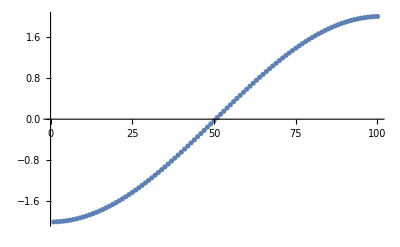

```mathematica
ListPlot[sortedEVals]
```

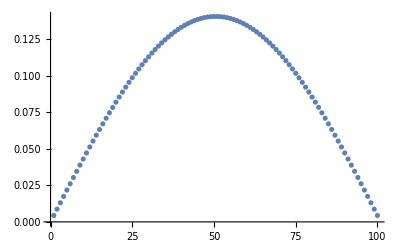
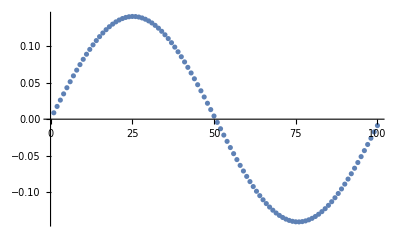
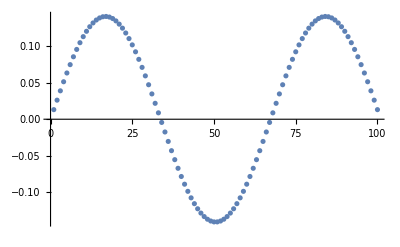
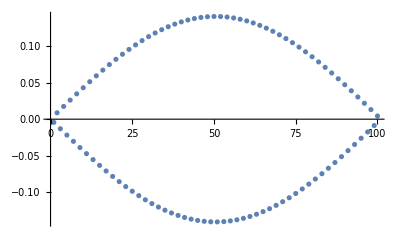

```mathematica
{ListPlot[sortedEVecs[[1]]],ListPlot[sortedEVecs[[2]]],ListPlot[sortedEVecs[[3]]],ListPlot[sortedEVecs[[100]]]}
```

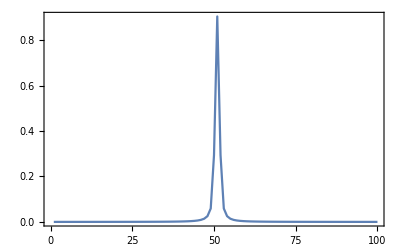
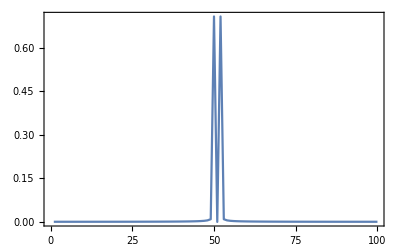
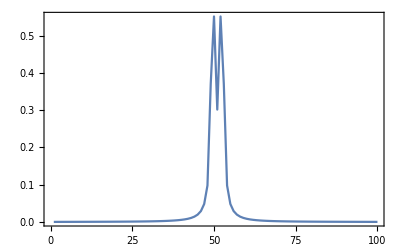
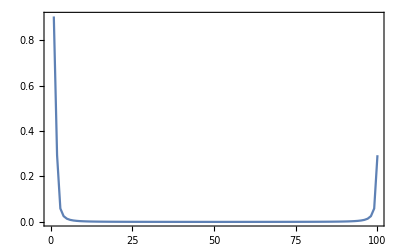

```mathematica
{ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[1]]]],50],PlotRange->All,Frame->True],
ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[2]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[3]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[100]]]],50],PlotRange->All,Frame->True]}
```

```mathematica
NDSolve
```

### With Trap

```mathematica
Ht[Nl_,ω_]:=Table[If[i==j,(i-Nl/2)^2 ω^2,If[Abs[i-j]==1,-1,0]],{i,1,Nl},{j,1,Nl}];
Ht[10,0.5]//MatrixForm
```

(4. | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 2.25 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1. | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0.25 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0. | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0.25 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1. | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 2.25 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 4. | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 6.25)

```mathematica
{EVals,EVecs}=Eigensystem[N[Ht[100,0.05]]];
```

```mathematica
sortedEVecs=(EVecs)[[Ordering[EVals]]];
sortedEVals=Sort[EVals];
```

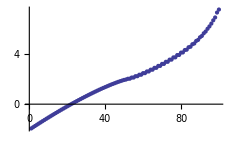

```mathematica
ListPlot[sortedEVals]
```

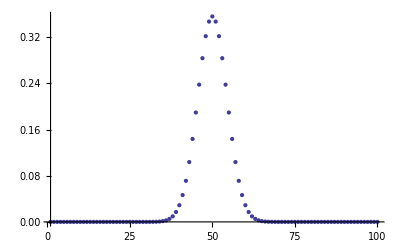
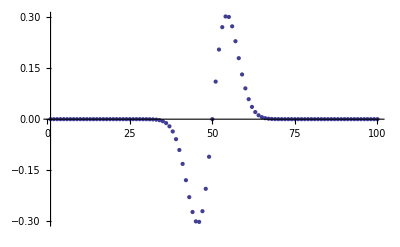
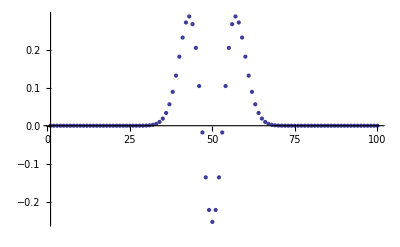
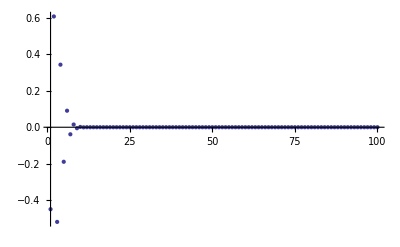
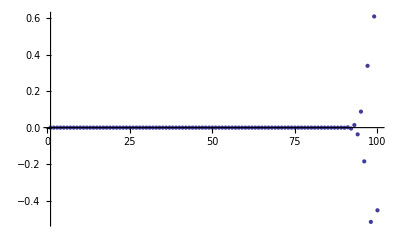

```mathematica
{ListPlot[sortedEVecs[[1]],PlotRange->All],
ListPlot[sortedEVecs[[2]],PlotRange->All],
ListPlot[sortedEVecs[[3]],PlotRange->All],
ListPlot[sortedEVecs[[99]],PlotRange->All],
ListPlot[sortedEVecs[[100]],PlotRange->All]}
```

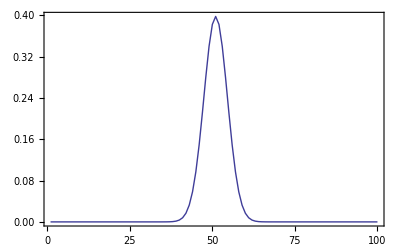
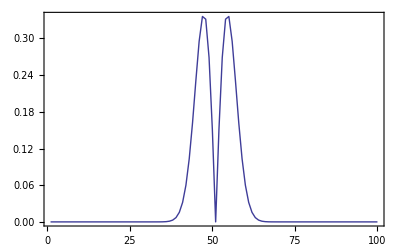
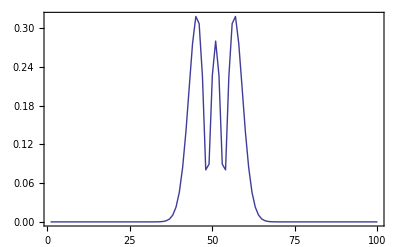
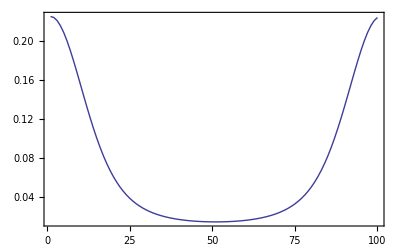

```mathematica
{ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[1]]]],50],PlotRange->All,Frame->True],
ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[2]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[3]]]],50],PlotRange->All,Frame->True],ListLinePlot[RotateRight[Abs[Fourier[sortedEVecs[[100]]]],50],PlotRange->All,Frame->True]}
```